# Pêndulo livre com controlo, com Runge-Kutta 4.aa ordem

```mathematica
ClearAll["Global`*"]
ClearAll[Subscript]
ClearAll[Derivative]
SetSystemOptions["SimplificationOptions"->"AutosimplifyTrigs"->False];
```

## Introdução de variáveis e funções de controlo

```mathematica
x[t_]:=fx[t]+l Cos[ϕ[t]]Sin[θ[t]];
y[t_]:=fy[t]+l Sin[ϕ[t]]Sin[θ[t]];
z[t_]:=l Cos[θ[t]];
```

## Lagrangeano do Pêndulo esférico com controlo

```mathematica
L=1/2 m(D[x[t],t]^2+D[y[t],t]^2+D[z[t],t]^2)-m g z[t]//FullSimplify;
```

## Equação de movimento

```mathematica
Substeta=First[Solve[D[D[L,θ'[t]],t]-D[L,θ[t]]==0,θ''[t]]//FullSimplify]
Subsphi=First[Solve[D[D[L,ϕ'[t]],t]-D[L,ϕ[t]]==0,ϕ''[t]]//FullSimplify]
Solve[D[D[L,fx'[t]],t]-D[L,fx[t]]==0/.Substeta/.Subsphi,fx''[t]]//FullSimplify
```

{θ''[t]→(g Sin[θ[t]]+Cos[θ[t]] (l Sin[θ[t]] ϕ'[t]^2-Cos[ϕ[t]] fx''[t]-Sin[ϕ[t]] fy''[t]))/l}

{ϕ''[t]→(Csc[θ[t]] (-2 l Cos[θ[t]] θ'[t] ϕ'[t]+Sin[ϕ[t]] fx''[t]-Cos[ϕ[t]] fy''[t]))/l}

{{fx''[t]→Csc[θ[t]] Sec[ϕ[t]] (-g Cos[θ[t]]+l θ'[t]^2+l Sin[θ[t]]^2 ϕ'[t]^2-Sin[θ[t]] Sin[ϕ[t]] fy''[t])}}

## Energia sem controlo

```mathematica
H=1/2 m(x'[t]^2+y'[t]^2+z'[t]^2)+m g z[t] /.{fy[t]->0,fx[t]->0,fx'[t]->0,fy'[t]->0}//FullSimplify
```

1/2 l m (2 g Cos[θ[t]]+l θ'[t]^2+l Sin[θ[t]]^2 ϕ'[t]^2)

```mathematica
Subscript[E, 1]=H/.θ[t]->0/.θ'[t]->0
```

g l m

## Controlo

```mathematica
(*EqsH={pθ'[t]->-D[H1,θ[t]], pϕ'[t]->-D[H1,ϕ[t]], θ'[t]->D[H1,pθ[t]], ϕ'[t]->D[H1,pϕ[t]]}//FullSimplify;*)
```

```mathematica
(*D[H,t]/.EqsH//FullSimplify*)
```

### Derivada da energia com as equações de movimento substituidas

```mathematica
D[H,t]/.Substeta/.Subsphi//FullSimplify
```

-l m (Sin[θ[t]] ϕ'[t] (-Sin[ϕ[t]] fx''[t]+Cos[ϕ[t]] fy''[t])+Cos[θ[t]] θ'[t] (Cos[ϕ[t]] fx''[t]+Sin[ϕ[t]] fy''[t]))

```mathematica
C1=D[H,t]/.Substeta/.Subsphi /.fy''[t]->fx''[t] Tan[ϕ[t]]/.fx''[t]->u Cos [ϕ[t]]l   //FullSimplify
```

-l^2 m u Cos[θ[t]] θ'[t]

```mathematica
C2=D[H,t]/.Substeta/.Subsphi/.fx''[t]->-fy''[t] Tan[ϕ[t]]/.fy''[t]->v Cos[ϕ[t]] l//FullSimplify//TrigFactor
```

-l^2 m v Sin[θ[t]] ϕ'[t]

### Parametros Físicos

```mathematica
paramFis={m->1,g->1,l->1,μ->0.4,ν->0.02};
```

```mathematica
(*paramFis={m->1,g->1,l->1,μ->0.3,ν->0.3};*)
```

## Integração numérica

## Equações do movimento

#### Parametros numéricos

```mathematica
Δt=0.001;
nMAX=20000;
```

```mathematica
(*For[Subscript[θ, RK4][0]=(3π)/4; Subscript[θ, RK4]'[0]=1; Subscript[ϕ, RK4][0]=0; Subscript[ϕ, RK4]'[0]=2; i2=0; i=0; v1x[0]=0; v1y[0]=0; Subscript[x1, RK4][0]=0; Subscript[y1, RK4][0]=0,i<nMAX,i++,*)
```

## Integração de θ̇, e ϕ̇ por Runge-Kutta 4.aa ordem e ϕ, θ por Euler

```mathematica
For[Subscript[θ, RK4][0]=(5π)/6; Subscript[θ, RK4]'[0]=0; Subscript[ϕ, RK4][0]=0; Subscript[ϕ, RK4]'[0]=0; i2=0; i=0; v1x[0]=0; v1y[0]=0; Subscript[x1, RK4][0]=0; Subscript[y1, RK4][0]=0,i<nMAX,i++,
If[i==0,Print[i]];
(*percentagem*)
If[(i-i2)/nMAX>0.1,Print[N[i*100/nMAX]];i2=i];

(*Funções de controlo u e v*)
Subscript[u, RK4][i]=-μ  Sign[Subscript[E, 1]-H] Sign[C1/(-m l^2 u)]/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;

(*Subscript[u, RK4][i]=-μ  (Subscript[E, 1]-H) (C1/(-m l^2 u))/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;*)

Subscript[ux, RK4][i]=Subscript[u, RK4][i]Cos[Subscript[ϕ, RK4][i]];
Subscript[v, RK4][i]=ν  Sign[C2/(-m l^2 v)]/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;
(*Subscript[v, RK4][i]=ν  C2/(-m l^2 v)/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;*)
Subscript[vy, RK4][i]=Subscript[v, RK4][i] Cos[Subscript[ϕ, RK4][i]];


A0={fx''[t]->fx1''[t]+fx2''[t],fy''[t]->fy1''[t]+fy2''[t]};
A1={fy1''[t]->fx1''[t]Tan[ϕ[t]],fx2''[t]->-fy2''[t]Tan[ϕ[t]]} ;
A2={fx1''[t]->l Subscript[ux, RK4][i],fy2''[t]->l Subscript[vy, RK4][i]};
ax[i]=Subscript[ux, RK4][i]-Subscript[vy, RK4][i]Tan[Subscript[ϕ, RK4][i]];
ay[i]=Subscript[ux, RK4] [i]Tan[Subscript[ϕ, RK4][i]]+Subscript[vy, RK4][i];

(*Runge-kutta para θ''[t]*)
fθ[i]=θ''[t]/.Substeta/.A0/.A1/.A2/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;

K1=fθ[i];
K2=fθ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K1,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K1,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K1,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K1,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K1,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K1};
K3=fθ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K2,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K2,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K2,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K2,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K2,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K2};
K4=fθ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt K3,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt K3,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt K3,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt K3,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt K3,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt K3};
(*Runge-Kutta para θ*)

nθ[i]=Subscript[θ, RK4]'[i];

N1=nθ[i];
N2=nθ[i]/.Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 N1;
N3=nθ[i]/.Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 N2;
N4=nθ[i]/.Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt N3;


(*Runge-kutta para ϕ'[t]*)
fϕ[i]=ϕ''[t]/.Subsphi/.A0/.A1/.A2/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}/.paramFis;

G1=fϕ[i];
G2=fϕ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K1,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K1,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K1,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K1,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K1,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K1};
G3=fϕ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt/2 K2,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt/2 K2,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 K2,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 K2,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 K2,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 K2};
G4=fϕ[i]/.{Subscript[θ, RK4]'[i]->Subscript[θ, RK4]'[i]+Δt K3,Subscript[θ, RK4][i]->Subscript[θ, RK4][i]+Δt K3,Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt K3,Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt K3,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt K3,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt K3};

(*Runge-Kutta para ϕ*)
mϕ[i]=Subscript[ϕ, RK4]'[i];

M1=mϕ[i];
M2=mϕ[i]/.Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 M1;
M3=mϕ[i]/.Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt/2 M2;
M4=mϕ[i]/.Subscript[ϕ, RK4]'[i]->Subscript[ϕ, RK4]'[i]+Δt M3;
(*Runge-Kutta para v1x*)
 P'[i]=ax[i];
P1=P'[i];
P2=P'[i]/.{Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 P1,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 P1,Subscript[vy, Rk4][i]->Subscript[vy, RK4][i]+Δt/2 P1};
P3=P'[i]/.{Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt/2 P2,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt/2 P2,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 P2};
P4=P'[i]/.{Subscript[ϕ, RK4][i]->Subscript[ϕ, RK4][i]+Δt P3,Subscript[ux, RK4][i]->Subscript[ux, RK4][i]+Δt P3,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt P3};

(*Runge-Kutta para v1y*)
V'[i]=ay[i];
V1=V'[i];
V2=V'[i]/.{Subscript[ϕ, RK4][t]->Subscript[ϕ, RK4][i]+Δt/2 V1,Subscript[ux, RK4][t]->Subscript[ux, RK4][i]+Δt/2 V1,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 V1};
V3=V'[i]/.{Subscript[ϕ, RK4][t]->Subscript[ϕ, RK4][i]+Δt/2 V2,Subscript[ux, RK4][t]->Subscript[ux, RK4][i]+Δt/2 V2,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt/2 V2};
V4=V'[i]/.{Subscript[ϕ, RK4][t]->Subscript[ϕ, RK4][i]+Δt V3,Subscript[ux, RK4][t]->Subscript[ux, RK4][i]+Δt V3,Subscript[vy, RK4][i]->Subscript[vy, RK4][i]+Δt V3};

(*Runge-Kutta para  posição para x*)
B=v1x[i];
X1=B;
X2=B/.v1x[i]->v1x[i]+Δt/2 X1;
X3=B/.v1x[i]->v1x[i]+Δt/2 X2;
X4=B/.v1x[i]->v1x[i]+Δt X3;

(*Runge-Kutta para  posição para y*)
A=v1y[i];
Y1=A;
Y2=A/.v1y[i]->v1y[i]+Δt/2 Y1;
Y3=A/.v1y[i]->v1y[i]+Δt/2 Y2;
Y4=A/.v1y[i]->v1y[i]+Δt Y3;

(*Próxima iteração*)
Subscript[θ, RK4]'[i+1]=Subscript[θ, RK4]'[i]+Δt/6(K1 +2 K2+2 K3+K4);
Subscript[θ, RK4][i+1]=Subscript[θ, RK4][i]+Δt/6(N1 +2 N2+2 N3+N4);
Subscript[ϕ, RK4]'[i+1]=Subscript[ϕ, RK4]'[i]+Δt/6(G1+2 G2+2 G3+G4);
Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4][i]+Δt/6(M1+2 M2+2 M3+M4);
v1x[i+1]=v1x[i]+Δt/6(P1+2 P2+2 P3+P4);
v1y[i+1]=v1y[i]+Δt/6(V1+2 V2+2 V3+V4);
Subscript[x1, RK4][i+1]=Subscript[x1, RK4][i]+Δt/6(X1+2 X2+2 X3+X4);
Subscript[y1, RK4][i+1]=Subscript[y1, RK4][i]+Δt/6(Y1+2 Y2+2 Y3+Y4);
Hi[i]=H/.{θ'[t]->Subscript[θ, RK4]'[i],θ[t]->Subscript[θ, RK4][i],ϕ'[t]->Subscript[ϕ, RK4]'[i],ϕ[t]->Subscript[ϕ, RK4][i]}

(*Condições Fronteira*)
If[Subscript[θ, RK4][i+1]>π,Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4][i+1]+π;Subscript[θ, RK4][i+1]=2π-Subscript[θ, RK4][i+1];Subscript[θ, RK4]'[i+1]=-Subscript[θ, RK4]'[i+1]];

If[Subscript[θ, RK4][i+1]<0,Subscript[ϕ, RK4][i+1]=Subscript[ϕ, RK4][i+1]+π ;  Subscript[θ, RK4][i+1]=-Subscript[θ, RK4][i+1] ; Subscript[θ, RK4]'[i+1]=-Subscript[θ, RK4]'[i+1]]]
```

0

ReplaceAll::reps: {Null (θ'[t]→0),Null (θ[t]→(5 π)/6),Null (ϕ'[t]→0),Null (ϕ[t]→0)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Null (θ'[t]→0.0005),Null (θ[t]→2.61799),Null (ϕ'[t]→2.5×10^-7),Null (ϕ[t]→0.)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

ReplaceAll::reps: {Null (θ'[t]→0.00134641),Null (θ[t]→2.61799),Null (ϕ'[t]→-0.00003975),Null (ϕ[t]→2.50125×10^-10)} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

10.005

20.01

30.015

40.02

50.025

60.03

70.035

80.04

90.045

```mathematica
(*Animate[Show[{Graphics3D[{Opacity[0.2],Sphere[{0,0,0}]}],{ListPointPlot3D[Table[{Cos[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Sin[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{n,0,n1,100}]]}}],{n1,0,nMAX,100},DefaultDuration->30,AnimationRunning->False]*)
```

```mathematica
(*Animate[Show[{Graphics3D[{Opacity[0.2],Sphere[{0,0,0}]}],{ListPointPlot3D[{{Cos[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Sin[Subscript[ϕ, RK4][n]] Sin[Subscript[θ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}}],{n,0,nMAX,100},DefaultDuration->30,AnimationRunning->False]*)
```

## Referencial Laboratório

```mathematica
SetDirectory["/home/nteixeira/S1_2018_2019/II/Presentation"]
```

/home/nteixeira/Desktop/S1_2018_2019/II/Presentation

```mathematica
Animate[Append[Show[Graphics3D[{Opacity[0.2],Sphere[{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0}]}],Graphics3D[Text["x",{1.6,0,0}]],
Graphics3D[Text["y",{0,1.6,0}]],
Graphics3D[Text["z",{0,0,1.6}]],Graphics3D[{Red,Arrow[{{0,0,0},{1.5,0,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,1.5,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,0,1.5}}]}](*,Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]+Sin[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{2Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],2Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],2Cos[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Sin[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Cos[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}]*),Graphics3D[{Green,Arrow[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{2 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],0}}]}],
Graphics3D[{Green,Arrow[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{-2 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[vy, RK4][n]+Subscript[y1, RK4][n],0}}]}],
Graphics3D[Text["o⃗",{2 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],-0.05}]],
Graphics3D[Text["s⃗",{-2 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[vy, RK4][n]+Subscript[y1, RK4][n],-0.05}]],Graphics3D[Line[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],Cos[Subscript[θ, RK4][n]]}}]],Graphics3D[{Yellow,Sphere[{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],Cos[Subscript[θ, RK4][n]]},0.1]}],
Graphics3D[Line[{{0,0,0},{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]}}]],
Graphics3D[{Green,Sphere[{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]},0.1]}],ListPointPlot3D[Table[{Sin[Subscript[θ, RK4][n1]]Cos[Subscript[ϕ, RK4][n1]]+Subscript[x1, RK4][n1],Sin[Subscript[θ, RK4][n1]]Sin[Subscript[ϕ, RK4][n1]]+Subscript[y1, RK4][n1],Cos[Subscript[θ, RK4][n1]]},{n1,0,n,50}]],ViewPoint->{2,2,2}],Boxed->False],{n,0,nMAX,50},DefaultDuration->60,AnimationRunning->False]
```

```mathematica
teste1=Append[Graphics3D[Sphere[]],Boxed->False];
i3=21;


Export[ToString[S1],teste1,ImageResolution->150];
```

```mathematica
For[n=0;i4=0,n <nMAX,n=n+50;i4=i4+1,

S1=StringForm["labrefgif0/labref0-``.png",i4];
Export[ToString[S1],Append[Show[Graphics3D[{Opacity[0.2],Sphere[{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0}]}],Graphics3D[Text["x",{1.6,0,0}]],
Graphics3D[Text["y",{0,1.6,0}]],
Graphics3D[Text["z",{0,0,1.6}]],Graphics3D[{Red,Arrow[{{0,0,0},{1.5,0,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,1.5,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,0,1.5}}]}](*,Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]+Sin[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{2Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],2Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],2Cos[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Sin[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Cos[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}]*),Graphics3D[{Green,Arrow[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{2 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],0}}]}],
Graphics3D[{Green,Arrow[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{-2 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[vy, RK4][n]+Subscript[y1, RK4][n],0}}]}],
Graphics3D[Text["o⃗",{2 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],-0.05}]],
Graphics3D[Text["s⃗",{-2 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n], 2 Subscript[vy, RK4][n]+Subscript[y1, RK4][n],-0.05}]],Graphics3D[Line[{{Subscript[x1, RK4][n],Subscript[y1, RK4][n],0},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],Cos[Subscript[θ, RK4][n]]}}]],Graphics3D[{Yellow,Sphere[{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+Subscript[x1, RK4][n],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Subscript[y1, RK4][n],Cos[Subscript[θ, RK4][n]]},0.1]}],
Graphics3D[Line[{{0,0,0},{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]}}]],
Graphics3D[{Green,Sphere[{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]},0.1]}],ListPointPlot3D[Table[{Sin[Subscript[θ, RK4][n1]]Cos[Subscript[ϕ, RK4][n1]]+Subscript[x1, RK4][n1],Sin[Subscript[θ, RK4][n1]]Sin[Subscript[ϕ, RK4][n1]]+Subscript[y1, RK4][n1],Cos[Subscript[θ, RK4][n1]]},{n1,0,n,50}]],ViewPoint->{2,2,2}],Boxed->False],ImageResolution->150]]
```

```mathematica
Flatten[{T1,T2}]
```

{0,1,2,3,4,5,6,7,8,9,10,10,9,8,7,6,5,4,3,2,1,0}

```mathematica
Directory[]
```

/home/nteixeira/Desktop/S1_2018_2019/II/Presentation

### Referencial do pivot

```mathematica
Animate[Append[Show[Graphics3D[{Opacity[0.2],Sphere[]}],Graphics3D[{Red,Arrow[{{0,0,0},{1.5,0,0}}]}],
Graphics3D[Text["x",{1.6,0,0}]],
Graphics3D[Text["y",{0,1.6,0}]],
Graphics3D[Text["z",{0,0,1.6}]],Graphics3D[{Red,Arrow[{{0,0,0},{0,1.5,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,0,1.5}}]}](*,Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]+Sin[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{2Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],2Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],2Cos[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Sin[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Cos[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}]*),(*Graphics3D[{Green,Arrow[{{0,0,0},{4 ax[n]+0, 4ay[n]+0,0}}]}],*)Graphics3D[Line[{{0,0,0},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+0,Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+0,Cos[Subscript[θ, RK4][n]]}}]],
Graphics3D[{Green,Arrow[{{0,0,0},{4 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]], 2 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]],0}}]}],
Graphics3D[{Green,Arrow[{{0,0,0},{-24 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]], 2 Subscript[vy, RK4][n],0}}]}],
Graphics3D[Text["o⃗",{4 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]], 4 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]],-0.05}]],
Graphics3D[Text["s⃗",{-4 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]], 4 Subscript[vy, RK4][n],-0.05}]],
Graphics3D[{Yellow,Sphere[{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+0,Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+0,Cos[Subscript[θ, RK4][n]]},0.1]}],
Graphics3D[Line[{{0,0,0},{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]}}]],
Graphics3D[{Green,Sphere[{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]},0.1]}],
ListPointPlot3D[Table[{Sin[Subscript[θ, RK4][n1]]Cos[Subscript[ϕ, RK4][n1]]+0,Sin[Subscript[θ, RK4][n1]]Sin[Subscript[ϕ, RK4][n1]]+0,Cos[Subscript[θ, RK4][n1]]},{n1,0,n,50}]],ViewPoint->{2,0.5,2}],Boxed->False],{n,0,nMAX,50},DefaultDuration->30,AnimationRunning->False]
```

```mathematica
For[n=0;i4=0,n <nMAX,n=n+50;i4=i4+1,

S2=StringForm["pivotrefgif0/pivotref0-``.png",i4];
Export[ToString[S2],Append[Show[Graphics3D[{Opacity[0.2],Sphere[]}],Graphics3D[{Red,Arrow[{{0,0,0},{1.5,0,0}}]}],
Graphics3D[Text["x",{1.6,0,0}]],
Graphics3D[Text["y",{0,1.6,0}]],
Graphics3D[Text["z",{0,0,1.6}]],Graphics3D[{Red,Arrow[{{0,0,0},{0,1.5,0}}]}],Graphics3D[{Red,Arrow[{{0,0,0},{0,0,1.5}}]}](*,Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]-Cos[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]+Sin[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{2Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],2Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],2Cos[Subscript[θ, RK4][n]]}}]}],Graphics3D[{Red,Arrow[{{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]-Sin[Subscript[ϕ, RK4][n]],Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+Cos[Subscript[ϕ, RK4][n]],Cos[Subscript[θ, RK4][n]]}}]}]*),(*Graphics3D[{Green,Arrow[{{0,0,0},{4 ax[n]+0, 4ay[n]+0,0}}]}],*)Graphics3D[Line[{{0,0,0},{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+0,Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+0,Cos[Subscript[θ, RK4][n]]}}]],
Graphics3D[{Green,Arrow[{{0,0,0},{2 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]], 2 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]],0}}]}],
Graphics3D[{Green,Arrow[{{0,0,0},{-2 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]], 2 Subscript[vy, RK4][n],0}}]}],
Graphics3D[Text["o⃗",{2 Subscript[u, RK4][n]Cos[Subscript[ϕ, RK4][n]], 2 Subscript[u, RK4][n]Sin[Subscript[ϕ, RK4][n]],-0.05}]],
Graphics3D[Text["s⃗",{-2 Subscript[vy, RK4][n]Tan[Subscript[ϕ, RK4][n]], 2 Subscript[vy, RK4][n],-0.05}]],
Graphics3D[{Yellow,Sphere[{Sin[Subscript[θ, RK4][n]]Cos[Subscript[ϕ, RK4][n]]+0,Sin[Subscript[θ, RK4][n]]Sin[Subscript[ϕ, RK4][n]]+0,Cos[Subscript[θ, RK4][n]]},0.1]}],
Graphics3D[Line[{{0,0,0},{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]}}]],
Graphics3D[{Green,Sphere[{Sin[Subscript[θ, RK4][0]]Cos[Subscript[ϕ, RK4][0]]+0,Sin[Subscript[θ, RK4][0]]Sin[Subscript[ϕ, RK4][0]]+0,Cos[Subscript[θ, RK4][0]]},0.1]}],
ListPointPlot3D[Table[{Sin[Subscript[θ, RK4][n1]]Cos[Subscript[ϕ, RK4][n1]]+0,Sin[Subscript[θ, RK4][n1]]Sin[Subscript[ϕ, RK4][n1]]+0,Cos[Subscript[θ, RK4][n1]]},{n1,0,n,50}]],ViewPoint->{2,3,3}],Boxed->False],ImageResolution->150]]
```

### θ[n] com o tempo

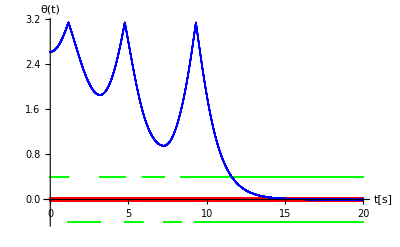

Null

```mathematica
Show[ListPlot[Table[{n*Δt ,Subscript[u, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20},{-0.4,π}},PlotLegends->Placed[PointLegend[{Green},{"o(t) control"}],{Right,Top}],AxesLabel->{"t[s]","θ(t)"},PlotStyle->{Green,Thickness->0.01}],ListPlot[Table[{n*Δt ,Subscript[v, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20},{-0.4,π}},PlotLegends->Placed[PointLegend[{Red},{"s(t) control"}],{Right,Top}],PlotStyle->{Red,Thickness->0.001}],ListPlot[Table[{n*Δt ,Subscript[θ, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20},{-0.4,π}},PlotLegends->Placed[PointLegend[{Blue},{"θ(t)"}],{Right,Top}],PlotStyle->Blue]]
```

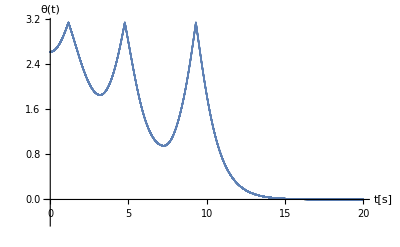

```mathematica
ListPlot[Table[{n*Δt ,Subscript[θ, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20},{-0.4,π}},AxesLabel->{"t[s]","θ(t)"}]
```

### variação θ’[n] com o tempo

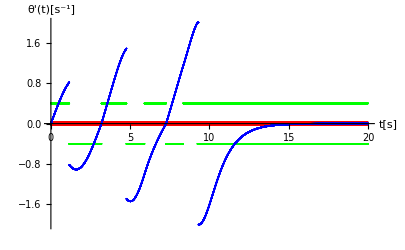

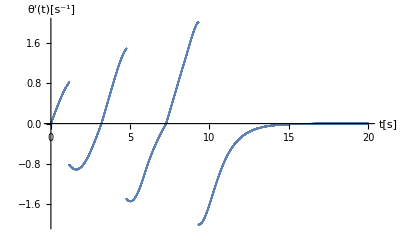

```mathematica
Show[ListPlot[Table[{n*Δt ,Subscript[u, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20},{-2,2}},PlotLegends->Placed[PointLegend[{Green},{"o(t) control"}],{Right,Top}],AxesLabel->{"t[s]","θ'(t)[s^-1]"},PlotStyle->{Green,Thickness->0.01}],ListPlot[Table[{n*Δt ,Subscript[v, RK4][n]},{n,0,nMAX}],PlotLegends->Placed[PointLegend[{Red},{"s(t) control"}],{Right,Top}],PlotStyle->{Red,Thickness->0.0001}],ListPlot[Table[{n*Δt ,Subscript[θ, RK4]'[n]},{n,0,nMAX}],PlotLegends->Placed[PointLegend[{Blue},{"θ'(t)"}],{Right,Top}],PlotStyle->Blue]]
ListPlot[Table[{n*Δt ,Subscript[θ, RK4]'[n]},{n,0,nMAX}],AxesLabel->{"t[s]","θ'(t)[s^-1]"}]
```

### Variação de ϕ’[n] com o tempo

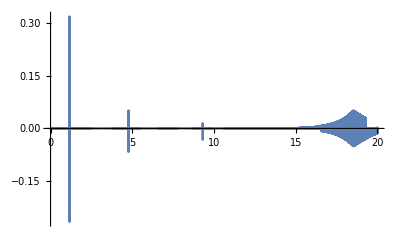

```mathematica
ListPlot[Table[{n*Δt ,Subscript[ϕ, RK4]'[n]},{n,0,nMAX}],PlotRange->All,Joined->True]
```

### Aceração do pivot ao longo do tempo

```mathematica
Animate[Show[(*Graphics[Arrow[{{0,0},{ax[n],ay[n]}}]],*)ListPlot[{ax[n],ay[n]},PlotRange->{{-1,1},{-1,1}}]],{n,0,nMAX,10},DefaultDuration->30,AnimationRunning->False]
```

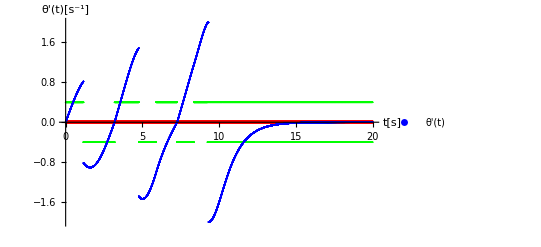

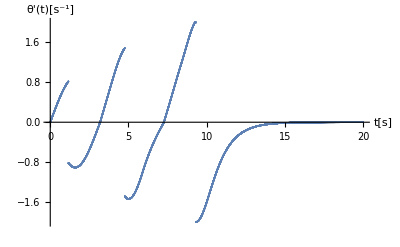

```mathematica
Show[ListPlot[Table[{n*Δt ,Subscript[u, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20},{-2,2}},PlotLegends->Placed[PointLegend[{Green},{"o control"}],{Right,Top}],AxesLabel->{"t[s]","θ'(t)[s^-1]"},PlotStyle->{Green,Thickness->0.01}],ListPlot[Table[{n*Δt ,Subscript[v, RK4][n]},{n,0,nMAX}],PlotLegends->Placed[PointLegend[{Red},{"s control"}],{Right,Top}],PlotStyle->{Red,Thickness->0.001}],ListPlot[Table[{n*Δt ,Subscript[θ, RK4]'[n]},{n,0,nMAX}],PlotLegends->PointLegend[{Blue},{"θ'(t)"}],PlotStyle->Blue]]
ListPlot[Table[{n*Δt ,Subscript[θ, RK4]'[n]},{n,0,nMAX}],AxesLabel->{"t[s]","θ'(t)[s^-1]"}]
```

### Posição do Pivot ao longo do tempo

```mathematica
Animate[ListPlot[Table[{Subscript[x1, RK4][n],Subscript[y1, RK4][n]},{n,0,n1,10}],PlotRange->{{0,10},{10,10}},AxesLabel->{"x[m]","y[m]"}],{n1,0,nMAX,10},DefaultDuration->30,AnimationRunning->False]
```

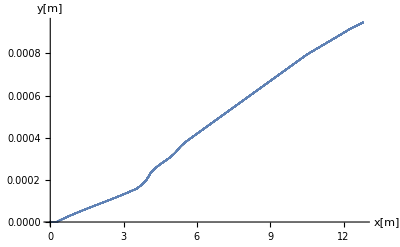

```mathematica
(*Show[ListPlot[Table[{n*Δt ,Subscript[u, RK4][n]},{n,0,nMAX}],PlotRange->{{-10,5},{2,-10}},PlotLegends->PointLegend[{Green},{"u control"}],AxesLabel->{"x[m]","y[m]"},PlotStyle->{Green,Thickness->0.01}],ListPlot[Table[{n*Δt ,Subscript[v, RK4][n]},{n,0,nMAX}],PlotLegends->PointLegend[{Red},{"v control"}],PlotStyle->{Red,Thickness->0.001}],ListPlot[Table[Subscript[x1, RK4][n],Subscript[y1, RK4][n]},{n,0,nMAX}],PlotLegends->PointLegend[{Blue},{"θ'(t)"}],PlotStyle->Blue]]*)
ListPlot[Table[{Subscript[x1, RK4][n],Subscript[y1, RK4][n]},{n,0,nMAX}],AxesLabel->{"x[m]","y[m]"}]
```

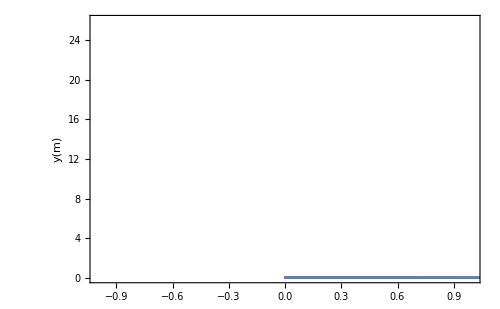

```mathematica
ListPlot[Table[{Subscript[x1, RK4][n],Subscript[y1, RK4][n]},{n,0,nMAX}],ImageSize->500,Axes->False,Frame->{{True,False},{False,True}},FrameLabel->{{"y(m)",None},{None,"x(m)"}},FrameTicks->All,PlotRange->{{0,0},{13,13}}]
```

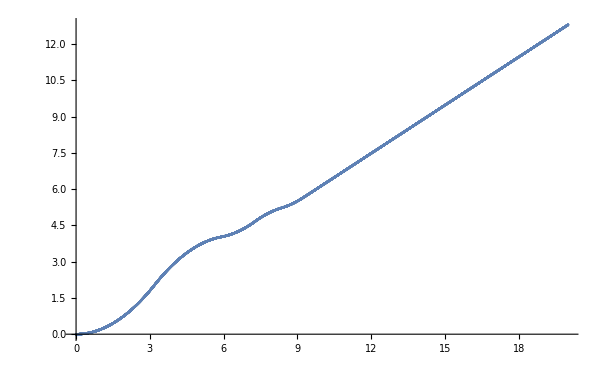

```mathematica
ListPlot[Table[{n*Δt,Subscript[x1, RK4][n]},{n,0,nMAX}]]
```

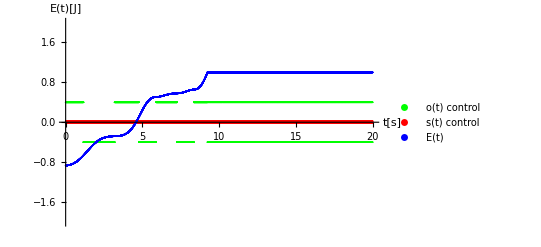

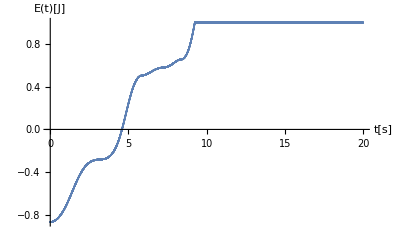

```mathematica
Show[ListPlot[Table[{n*Δt ,Subscript[u, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20},{-2,2}},PlotLegends->Placed[PointLegend[{Green},{"o(t) control"}],{Left,Bottom}],AxesLabel->{"t[s]","E(t)[J]"},PlotStyle->{Green,Thickness->0.01}],ListPlot[Table[{n*Δt ,Subscript[v, RK4][n]},{n,0,nMAX}],PlotLegends->Placed[PointLegend[{Red},{"s(t) control"}],{Center,Bottom}],PlotStyle->{Red,Thickness->0.001}],ListPlot[Table[{a*Δt ,H/.{θ'[t]->Subscript[θ, RK4]'[a],θ[t]->Subscript[θ, RK4][a],ϕ'[t]->Subscript[ϕ, RK4]'[a],ϕ[t]->Subscript[ϕ, RK4][a]}/.paramFis},{a,0,nMAX}],PlotLegends->Placed[PointLegend[{Blue},{"E(t)"}],{Right,Bottom}],PlotStyle->Blue]]
ListPlot[Table[{a*Δt ,H/.{θ'[t]->Subscript[θ, RK4]'[a],θ[t]->Subscript[θ, RK4][a],ϕ'[t]->Subscript[ϕ, RK4]'[a],ϕ[t]->Subscript[ϕ, RK4][a]}/.paramFis},{a,0,nMAX}],AxesLabel->{"t[s]","E(t)[J]"}]
```

```mathematica
Subscript[θ, RK4][20000]
```

0.00134269

```mathematica
V1
```

-0.0177676

```mathematica
Subscript[θ, RK4][10]
```

2.61803

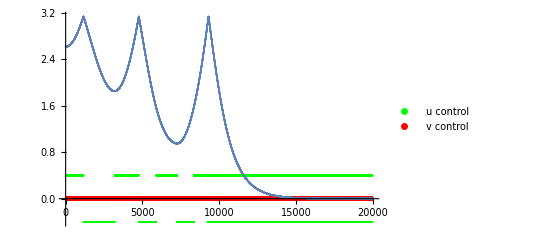

```mathematica
Show[ListPlot[Table[{n,Subscript[u, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20000},{-0.4,π}},PlotLegends->PointLegend[{Green},{"u control"}],PlotStyle->{Green,Thickness->0.01}],ListPlot[Table[{n,Subscript[v, RK4][n]},{n,0,nMAX}],PlotRange->{{0,20000},{-0.4,π}},PlotLegends->PointLegend[{Red},{"v control"}],PlotStyle->{Red,Thickness->0.001}],ListPlot[Table[{n,Subscript[θ, RK4][n]},{n,0,nMAX}]]]
```

```mathematica
PointLegend[{Red},{"u control"}]
```